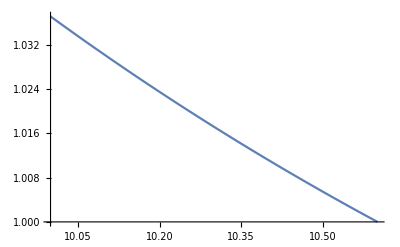

```mathematica
kmin=10.1;
kmax=kmin+0.001;
dk=kmax-kmin;
Ng1[Eb_]:=4/3 Log[kmax/kmin]/dk;
Ng2[Eb_]:=-(4(kmax-kmin))/(3 Eb)/dk;
Ng3[Eb_]:=(kmax^2-kmin^2)/(2 Eb^2)/dk;

Ng[Eb_]:=4/3 Log[kmax/kmin]-(4(kmax-kmin))/(3 Eb)+(kmax^2-kmin^2)/(2 Eb^2);
Ngnorm[Eb_]:=Ng[Eb]/Ng[10.6];
Plot[Ngnorm[E],{E,10.0,10.6}]
```

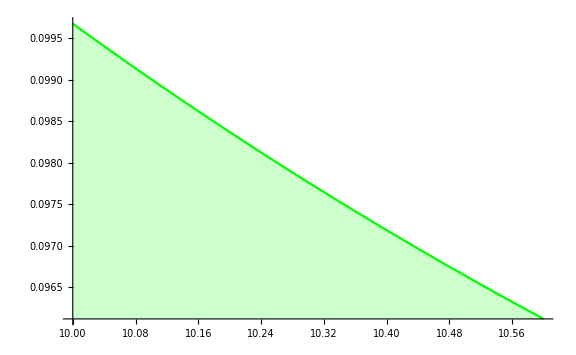

```mathematica
Plot[{Ng1[Eb]+Ng2[Eb]+Ng3[Eb]},{Eb,10.0,10.6},
Filling->Axis,
PlotStyle->{Red,Blue,Green},ImageSize->Large]
```

```mathematica
Plot[{(4/3-4/3 (k/Eb)+(k/Eb)^2)/k},{k,10.,10.6},
Filling->Axis,
PlotStyle->{Red,Blue,Green},ImageSize->Large]
```

```mathematica
dsdk[k_,Eb_]:=If[k<Eb,((4/3-4/3 (k/Eb)+(k/Eb)^2)/k)/k,0];
```

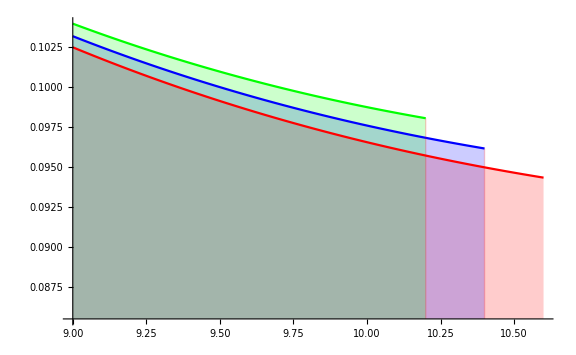

```mathematica
Plot[{dsdk[k,10.6],dsdk[k,10.4],dsdk[k,10.2]},{k,9,10.6},Filling->Axis,
PlotStyle->{Red,Blue,Green},ImageSize->Large]
```

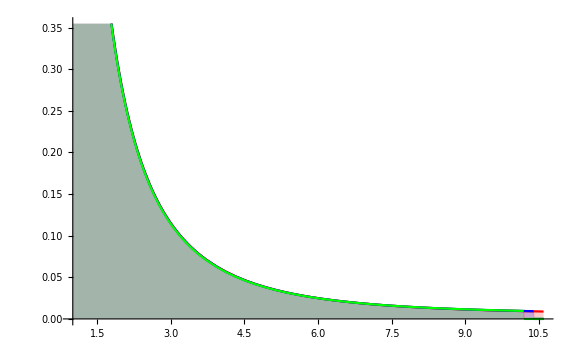

```mathematica
Plot[{dsdk[k,10.6],dsdk[k,10.4],dsdk[k,10.2]},{k,1,10.6},Filling->Axis,
PlotStyle->{Red,Blue,Green},ImageSize->Large]
```

```mathematica
M0=(
ds[k_,E0_]:=1/k(
(1+((E0-k)/E0)^2-2/3(E0-k)/E0)(-Log[(k/(2 E0 (E0-k)))^2+(1/111)^2]+1-2 111k/(2 E0(E0-k)) Arc
```